# 2022-07-20

Performing the Sudakov integrals for different splitting functions

## Perform θ-integration

```mathematica
Integrate[1/θ,{θ,pt0/(z*pt1),1},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z}]
```

Log[(pt1 z)/pt0]

## Perform z-integration

## P[z] = 1/z

```mathematica
PgtoggGavin[z_]:=1/z;
```

```mathematica
Integrate[PgtoggGavin[z]Log[(pt1 z)/pt0],{z, pt0/pt1,1},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z}]
```

1/2 Log[pt0/pt1]^2

```mathematica
SudakovGavin[pt1_,pt0_]:=1/2 Log[pt0/pt1]^2
```

```mathematica
ExpSudakovGavin[pt1_,pt0_,CA_,αs_]:=Exp[-(2αs*CA)/π SudakovGavin[pt1,pt0]]
```

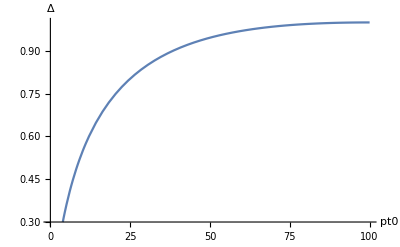

```mathematica
Plot[ExpSudakovGavin[100,pt0,3,0.12],{pt0,0.001,100},AxesLabel->{"pt0","Δ"}]
```

## P[z] = (1-z)/z+(z-z^2)/2

```mathematica
Pgtoggnonsym[z_]:=((1-z)/z+(z-z^2)/2);
```

```mathematica
Integrate[Pgtoggnonsym[z]Log[(pt1 z)/pt0],{z, pt0/pt1,1},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z}]
```

1/72 (-((pt0-pt1) (4 pt0^2-5 pt0 pt1+67 pt1^2))/pt1^3+6 Log[pt0/pt1] (11+6 Log[pt0/pt1]))

```mathematica
Sudakovnonsym[pt1_,pt0_]:=1/72 (-((pt0-pt1) (4 pt0^2-5 pt0 pt1+67 pt1^2))/pt1^3+6 Log[pt0/pt1] (11+6 Log[pt0/pt1]))
```

```mathematica
ExpSudakovnonsym[pt1_,pt0_,CA_,αs_]:=Exp[-(2αs*CA)/π Sudakovnonsym[pt1,pt0]]
```

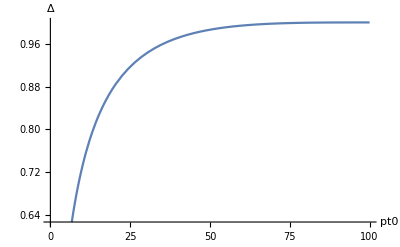

```mathematica
Plot[ExpSudakovnonsym[100,pt0,3,0.12],{pt0,0.001,100},AxesLabel->{"pt0","Δ"}]
```

## P[z] = (1-z)/z+(z-z^2)/2

```mathematica
Pgtoggnonsym[z_]:=((1-z)/z+(z-z^2)/2);
```

```mathematica
Integrate[Pgtoggnonsym[z]Log[(pt1 z)/pt0],{z, pt0/pt1,1},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z}]
```

1/72 (-((pt0-pt1) (4 pt0^2-5 pt0 pt1+67 pt1^2))/pt1^3+6 Log[pt0/pt1] (11+6 Log[pt0/pt1]))

```mathematica
Sudakovnonsym[pt1_,pt0_]:=1/72 (-((pt0-pt1) (4 pt0^2-5 pt0 pt1+67 pt1^2))/pt1^3+6 Log[pt0/pt1] (11+6 Log[pt0/pt1]))
```

```mathematica
ExpSudakovnonsym[pt1_,pt0_,CA_,αs_]:=Exp[-(2αs*CA)/π Sudakovnonsym[pt1,pt0]]
```

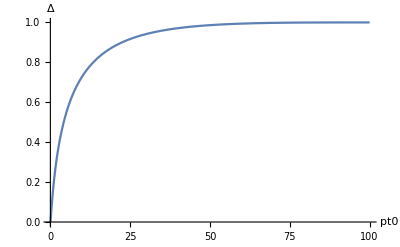

```mathematica
Plot[ExpSudakovnonsym[100,pt0,3,0.12],{pt0,0.001,100},AxesLabel->{"pt0","Δ"},PlotRange->All]
```

```mathematica
Solve[-z(z-1)pt1/pt0==1,z]//Simplify
```

{{z→(pt1-√(pt1 (-4 pt0+pt1)))/(2 pt1)},{z→(pt1+√(pt1 (-4 pt0+pt1)))/(2 pt1)}}

```mathematica
(1-√(-4 pt0/pt1+1))/2
```

1/2 (1-√(1-(4 pt0)/pt1))

```mathematica
Series[1/2-(√(-4 ϵ+1))/2,{ϵ,0,1}]
```

ϵ+O[ϵ]^2

## P[z] = (1-z)/z+z/(1-z)+z-z^2the version of Sohyun and Gian-Michele

here, the splitting function is symmetric in z -> 1-z but the boundary of the angular integral is not (that’s why the integrand is Log[(pt1 z)/pt0] and not Log[(pt1 z (1-z))/pt0]

```mathematica
PgtoggsymUrs[z_]:=((1-z)/z+z/(1-z)+z-z^2);
```

```mathematica
Integrate[PgtoggsymUrs[z]Log[(pt1 z)/pt0],{z, pt0/pt1,1/2},Assumptions->{pt0∈ Reals,pt1∈ Reals , pt1>pt0, pt0>0,z<1, z>0, pt0!=pt1*0.5,pt0<pt1 z,2 pt0<pt1}]
```

137/144-π^2/4-pt0^3/(9 pt1^3)+pt0^2/(4 pt1^2)-(2 pt0)/pt1+(11 Log[2])/12-2 Log[2]^2+1/4 Log[2] Log[256]+((pt0 (2 pt0^2-3 pt0 pt1+12 pt1^2))/(6 pt1^3)+Log[1-pt0/pt1]) Log[pt0/pt1]-1/2 Log[pt0/pt1]^2-Log[pt1]^2-11/12 Log[pt1/pt0]+(pt0^3 Log[pt1/pt0])/(3 pt1^3)-(pt0^2 Log[pt1/pt0])/(2 pt1^2)+(2 pt0 Log[pt1/pt0])/pt1+Log[2] Log[pt1/pt0]+1/3 Log[8] Log[pt1/pt0]-2 Log[2-(2 pt0)/pt1] Log[pt1/pt0]+2 Log[1-pt0/pt1] Log[pt1/pt0]-Log[-pt0/(pt0-pt1)] Log[pt1/pt0]+ⅈ π Log[pt1/(-pt0+pt1)]+Log[pt0] Log[pt1/(-pt0+pt1)]+1/2 Log[pt1/(-pt0+pt1)]^2+Log[pt1] Log[-pt0+pt1]+PolyLog[2,-pt1/(pt0-pt1)]

```mathematica
SudakovsymUrs[pt1_,pt0_]:=137/144-π^2/4-pt0^3/(9 pt1^3)+pt0^2/(4 pt1^2)-(2 pt0)/pt1+(11 Log[2])/12-2 Log[2]^2+1/4 Log[2] Log[256]+((pt0 (2 pt0^2-3 pt0 pt1+12 pt1^2))/(6 pt1^3)+Log[1-pt0/pt1]) Log[pt0/pt1]-1/2 Log[pt0/pt1]^2-Log[pt1]^2-11/12 Log[pt1/pt0]+(pt0^3 Log[pt1/pt0])/(3 pt1^3)-(pt0^2 Log[pt1/pt0])/(2 pt1^2)+(2 pt0 Log[pt1/pt0])/pt1+Log[2] Log[pt1/pt0]+1/3 Log[8] Log[pt1/pt0]-2 Log[2-(2 pt0)/pt1] Log[pt1/pt0]+2 Log[1-pt0/pt1] Log[pt1/pt0]-Log[-pt0/(pt0-pt1)] Log[pt1/pt0]+ⅈ π Log[pt1/(-pt0+pt1)]+Log[pt0] Log[pt1/(-pt0+pt1)]+1/2 Log[pt1/(-pt0+pt1)]^2+Log[pt1] Log[-pt0+pt1]+PolyLog[2,-pt1/(pt0-pt1)]
```

```mathematica
ExpSudakovsymUrs[pt1_,pt0_,CA_,αs_]:=Exp[-(4*αs*CA)/π SudakovsymUrs[pt1,pt0]]
```

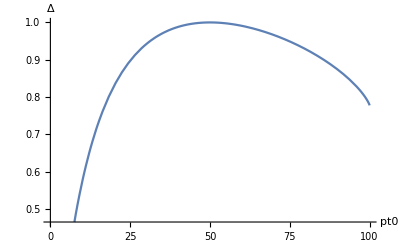

```mathematica
Plot[ExpSudakovsymUrs[100,pt0,3,0.12],{pt0,0.001,100},AxesLabel->{"pt0","Δ"}]
```

## P[z] = (1-z)/z+z/(1-z)+z-z^2 (version of Urs)

Here, Urs explores what happens if the splitting function is kept symmetric but the angular integral has a symmetric boundary (see integrand tern Log[(pt1 z*(1-z))/pt0]) and the boundary of the z-integration is obtained from requiring z(1-z) pt1 > pt0 which leads to zlow and zhigh has boundaries

```mathematica
PgtoggsymUrs[z_]:=((1-z)/z+z/(1-z)+z-z^2);
```

```mathematica
zlow=1/2 (1-√(1-(4 pt0)/pt1))
zhigh=1/2 (1+√(1-(4 pt0)/pt1))
```

since mathematic would like to know that boundaries are real, I do the calculation for zl, zh and I then insert zlow, zhigh into the result

```mathematica
Integrate[PgtoggsymUrs[z]Log[(pt1 z*(1-z))/pt0],{z,zl,zh},Assumptions->{pt0∈ Reals,pt1∈ Reals ,zl ∈ Reals ,zh ∈ Reals ,zl>0,zh>zl,zh<1,pt1>pt0, pt0>0,z<1, z>0, pt0<pt1 z(1-z)}]
```

1/18 (69 zh-6 zh^2+4 zh^3-69 zl+6 zl^2-4 zl^3-3 Log[1-zh]-36 zh Log[zh]+9 zh^2 Log[zh]-6 zh^3 Log[zh]+9 Log[zh]^2+36 Log[(pt1-pt1 zh)/pt0]-36 zh Log[(pt1-pt1 zh)/pt0]+9 zh^2 Log[(pt1-pt1 zh)/pt0]-6 zh^3 Log[(pt1-pt1 zh)/pt0]+18 Log[zh] Log[(pt1-pt1 zh)/pt0]-9 Log[(pt1-pt1 zh)/pt0]^2+3 Log[1-zl]+36 zl Log[zl]-9 zl^2 Log[zl]+6 zl^3 Log[zl]-9 Log[zl]^2-36 Log[(pt1-pt1 zl)/pt0]+36 zl Log[(pt1-pt1 zl)/pt0]-9 zl^2 Log[(pt1-pt1 zl)/pt0]+6 zl^3 Log[(pt1-pt1 zl)/pt0]-18 Log[zl] Log[(pt1-pt1 zl)/pt0]+9 Log[(pt1-pt1 zl)/pt0]^2+36 PolyLog[2,1-zh]-36 PolyLog[2,1-zl])

```mathematica
SudakovsymUrs[pt1_,pt0_]:=1/18 (69 zh-6 zh^2+4 zh^3-69 zl+6 zl^2-4 zl^3-3 Log[1-zh]-36 zh Log[zh]+9 zh^2 Log[zh]-6 zh^3 Log[zh]+9 Log[zh]^2+36 Log[(pt1-pt1 zh)/pt0]-36 zh Log[(pt1-pt1 zh)/pt0]+9 zh^2 Log[(pt1-pt1 zh)/pt0]-6 zh^3 Log[(pt1-pt1 zh)/pt0]+18 Log[zh] Log[(pt1-pt1 zh)/pt0]-9 Log[(pt1-pt1 zh)/pt0]^2+3 Log[1-zl]+36 zl Log[zl]-9 zl^2 Log[zl]+6 zl^3 Log[zl]-9 Log[zl]^2-36 Log[(pt1-pt1 zl)/pt0]+36 zl Log[(pt1-pt1 zl)/pt0]-9 zl^2 Log[(pt1-pt1 zl)/pt0]+6 zl^3 Log[(pt1-pt1 zl)/pt0]-18 Log[zl] Log[(pt1-pt1 zl)/pt0]+9 Log[(pt1-pt1 zl)/pt0]^2+36 PolyLog[2,1-zh]-36 PolyLog[2,1-zl])//.zl->1/2 (1-√(1-(4 pt0)/pt1))//.zh->1/2 (1+√(1-(4 pt0)/pt1))
```

compared to the Gian-Michele and Sohyun version I change the prefactor in the exponent by a factor 2 since I have integrated over two singularities (z->0 and z-> 1) while Gian-Michele and Sohyun integrated only over one singularity. I expect that with this choice, the double log comes with the same prefactor in both calculations

```mathematica
ExpSudakovsymUrs[pt1_,pt0_,CA_,αs_]:=Exp[-(2*αs*CA)/π SudakovsymUrs[pt1,pt0]]
```

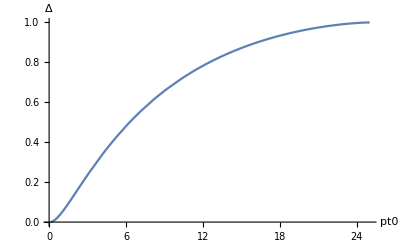

```mathematica
Plot[ExpSudakovsymUrs[100,pt0,3,0.12],{pt0,0.1,100},AxesLabel->{"pt0","Δ"},PlotRange->All]
```

The issue is obvious: with the choice zlow=1/2 (1-√(1-(4 pt0)/pt1)), one restricts onself to pt0 < pt1/4 and that’s why the plot below stops now at 25 GeV. This is physically unwanted though it seems to be technically correct. There is clearly expert knowledge needed to know which tricks  work and which do not ...

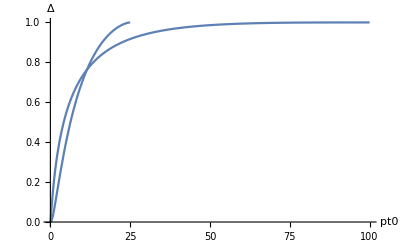

```mathematica
Show[-Graphics-,-Graphics-]
```

## Plot together

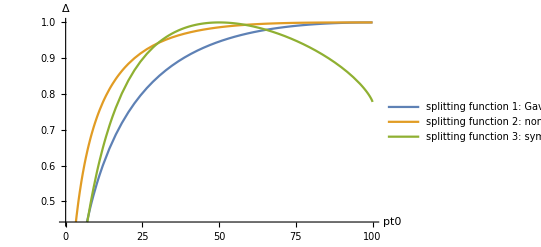

```mathematica
Plot[{ExpSudakovGavin[100,pt0,3,0.12],ExpSudakovnonsym[100,pt0,3,0.12],ExpSudakovsymUrs[100,pt0,3,0.12]},{pt0,0.001,100},AxesLabel->{"pt0","Δ"},PlotLegends->{"splitting function 1: Gavin (Eq. 25)","splitting function 2: non-sym (Eq. 27)","splitting function 3: sym (Eq. 29)"}]
```

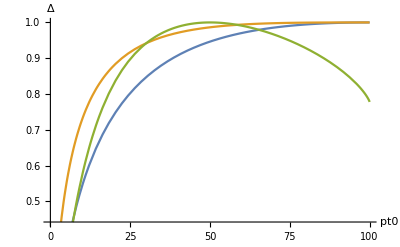
```mathematica
Show[-Graphics-,-Graphics-]
```